```mathematica
prec=15;
```

```mathematica
χ[{L1_,L2_},r_][k_]:=Module[{},
If[r==1,
Return[HeavisideTheta[k-1/2]-HeavisideTheta[k-L1-1/2],Module];
];
If[r==2,
Return[HeavisideTheta[k-L1-1/2]-HeavisideTheta[k-L1-L2-1/2],Module];
];
];
```

```mathematica
J[{L1_,L2_},{p1_,p2_}][k_]:=Outer[Times, {(L2 p1- L1 p2)/(L1+L2)}//Flatten,((χ[{L1,L2},1][k])/L1-(χ[{L1,L2},2][k])/L2)]
```

```mathematica
RedJ[{L1_,L2_},{p1_,p2_}][k_]:=Outer[Times, {(L2 p1- L1 p2)/(L1+L2)}//Flatten,{((χ[{L1,L2},1][k])/L1-(χ[{L1,L2},2][k])/L2+1/L2)}//Flatten]
```

```mathematica
Jvector[{L1_,L2_},{p1_,p2_}]:=J[{L1,L2},{p1,p2}][Range[1,L1+L2]]
```

```mathematica
RedJvector[{L1_,L2_},{p1_,p2_}]:=RedJ[{L1,L2},{p1,p2}][Range[1,L1+L2-1]]
```

```mathematica
Mkernelfunc[L_,x_]:=(-Sin[Pi/L](*+(-1)^x(Cos[Pi/L]-Exp[2Pi I *x/L])*))/(Cos[Pi/L]-Cos[2Pi x/L])
```

```mathematica
MMatrix[{L1_,L2_}]:=Module[{Mkernel,Mkernel1,Mkernel2,k1,k2,M,L=L1+L2},
Mkernel=Table[Mkernelfunc[L,x],{x,0,L-1}];
Mkernel1=Table[Mkernelfunc[L1,x],{x,0,L1-1}];
Mkernel2=Table[Mkernelfunc[L2,x],{x,0,L2-1}];
k1=Table[k*χ[{L1,L2},1][k],{k,1,L}];
k2=Table[(k-L1)*χ[{L1,L2},2][k],{k,1,L}];

M=Table[
(*multiply by Pi to kill exponential scaling of det*)
Pi(1/(Pi*L)Mkernel[[Mod[k-l,L]+1]]+(χ[{L1,L2},1][k]χ[{L1,L2},1][l])/(Pi*L1)Mkernel1[[Mod[k1[[k]]-k1[[l]],L1]+1]]+(χ[{L1,L2},2][k]χ[{L1,L2},2][l])/(Pi*L2)Mkernel2[[Mod[k2[[k]]-k2[[l]],L2]+1]])
,{k,1,L},
{l,1,L}];
Return[M,Module];
];
```

```mathematica
MMatrixN[{L1_,L2_}]:=Module[{Mkernel,Mkernel1,Mkernel2,k1,k2,M,L=L1+L2},
Mkernel=Table[N[Mkernelfunc[L,x],prec],{x,0,L-1}];
Mkernel1=Table[N[Mkernelfunc[L1,x],prec],{x,0,L1-1}];
Mkernel2=Table[N[Mkernelfunc[L2,x],prec],{x,0,L2-1}];
k1=Table[k*χ[{L1,L2},1][k],{k,1,L}];
k2=Table[(k-L1)*χ[{L1,L2},2][k],{k,1,L}];

M=Table[
(*multiply by Pi to kill exponential scaling of det*)
Pi*N[1/(Pi*L)Mkernel[[Mod[k-l,L]+1]]+(χ[{L1,L2},1][k]χ[{L1,L2},1][l])/(Pi*L1)Mkernel1[[Mod[k1[[k]]-k1[[l]],L1]+1]]+(χ[{L1,L2},2][k]χ[{L1,L2},2][l])/(Pi*L2)Mkernel2[[Mod[k2[[k]]-k2[[l]],L2]+1]],prec]
,{k,1,L},
{l,1,L}];
Return[M,Module];
];
```

```mathematica
RedMMatrixN[{L1_,L2_}]:=Module[{Mkernel,Mkernel1,Mkernel2,LastRow,k1,k2,M,L=L1+L2},
Mkernel=Table[N[Mkernelfunc[L,x],prec],{x,0,L-1}];
Mkernel1=Table[N[Mkernelfunc[L1,x],prec],{x,0,L1-1}];
Mkernel2=Table[N[Mkernelfunc[L2,x],prec],{x,0,L2-1}];
k1=Table[k*χ[{L1,L2},1][k],{k,1,L}];
k2=Table[(k-L1)*χ[{L1,L2},2][k],{k,1,L}];
LastRow=Table[Pi*N[1/(Pi*L)Mkernel[[Mod[k-L,L]+1]]+(χ[{L1,L2},1][k]χ[{L1,L2},1][L])/(Pi*L1)Mkernel1[[Mod[k1[[k]]-k1[[L]],L1]+1]]+(χ[{L1,L2},2][k]χ[{L1,L2},2][L])/(Pi*L2)Mkernel2[[Mod[k2[[k]]-k2[[L]],L2]+1]],prec],{k,1,L}];
M=Table[
(*multiply by Pi to kill exponential scaling of det*)
Pi*N[1/(Pi*L)Mkernel[[Mod[k-l,L]+1]]+(χ[{L1,L2},1][k]χ[{L1,L2},1][l])/(Pi*L1)Mkernel1[[Mod[k1[[k]]-k1[[l]],L1]+1]]+(χ[{L1,L2},2][k]χ[{L1,L2},2][l])/(Pi*L2)Mkernel2[[Mod[k2[[k]]-k2[[l]],L2]+1]],prec]-LastRow[[k]]-LastRow[[l]]+LastRow[[L]]
,{k,1,L-1},
{l,1,L-1}];
Return[M,Module];
];
```

```mathematica
RedJMJ[{L1_,L2_}]:=Module[{MInv,L=L1+L2},
MInv = Inverse[RedMMatrixN[{L1,L2}]];
Return[1/L^2 Total[Total[MInv[[1;;L1,1;;L1]]]]]
]
```

### Some random tests

```mathematica
Monitor[Table[{2k,RedJMJ[{2k,200-2k}]},{k,1,50}],k]
```

{{2,0.0002022779006551},{4,0.00066171563345778},{6,0.0013218978872708},{8,0.0021498451230951},{10,0.0031212826433785},{12,0.004216703243534},{14,0.0054196687828188},{16,0.0067159095541917},{18,0.0080927850244039},{20,0.0095389335570937},{22,0.011044031112485},{24,0.012598617440543},{26,0.014193966427642},{28,0.015821986609898},{30,0.017475143038664},{32,0.01914639470983},{34,0.020829143622932},{36,0.022517192717363},{38,0.024204710710794},{40,0.025886202391801},{42,0.027556483284628},{44,0.029210657863738},{46,0.030844100683767},{48,0.032452439928899},{50,0.034031542989172},{52,0.035577503749749},{54,0.03708663133948},{56,0.038555440131984},{58,0.039980640829303},{60,0.041359132487411},{62,0.042687995366297},{64,0.043964484506238},{66,0.045186023947278},{68,0.046350201521608},{70,0.047454764158954},{72,0.048497613653811},{74,0.049476802850639},{76,0.050390532209291},{78,0.051237146718181},{80,0.052015133127144},{82,0.052723117475802},{84,0.053359862896573},{86,0.053924267674361},{88,0.05441536354753},{90,0.054832314237018},{92,0.055174414192492},{94,0.055441087546264},{96,0.055631887267349},{98,0.055746494509628},{100,0.055784718149475}}

```mathematica
fp1Plus=%341
```

{{2,0.0002022779006551},{4,0.00066171563345778},{6,0.0013218978872708},{8,0.0021498451230951},{10,0.0031212826433785},{12,0.004216703243534},{14,0.0054196687828188},{16,0.0067159095541917},{18,0.0080927850244039},{20,0.0095389335570937},{22,0.011044031112485},{24,0.012598617440543},{26,0.014193966427642},{28,0.015821986609898},{30,0.017475143038664},{32,0.01914639470983},{34,0.020829143622932},{36,0.022517192717363},{38,0.024204710710794},{40,0.025886202391801},{42,0.027556483284628},{44,0.029210657863738},{46,0.030844100683767},{48,0.032452439928899},{50,0.034031542989172},{52,0.035577503749749},{54,0.03708663133948},{56,0.038555440131984},{58,0.039980640829303},{60,0.041359132487411},{62,0.042687995366297},{64,0.043964484506238},{66,0.045186023947278},{68,0.046350201521608},{70,0.047454764158954},{72,0.048497613653811},{74,0.049476802850639},{76,0.050390532209291},{78,0.051237146718181},{80,0.052015133127144},{82,0.052723117475802},{84,0.053359862896573},{86,0.053924267674361},{88,0.05441536354753},{90,0.054832314237018},{92,0.055174414192492},{94,0.055441087546264},{96,0.055631887267349},{98,0.055746494509628},{100,0.055784718149475}}

{{1/100,-12.839170829333},{1/50,-10.610660608959},{3/100,-9.5228358874475},{1/25,-8.8088466247567},{1/20,-8.2792449308898},{3/50,-7.8592776309514},{7/100,-7.5120037648262},{2/25,-7.2165167628209},{9/100,-6.9598528288935},{1/10,-6.7334255958772},{11/100,-6.531257236871},{3/25,-6.3490202347619},{13/100,-6.1834818032085},{7/50,-6.0321638249342},{3/20,-5.8931252797395},{4/25,-5.7648178098524},{17/100,-5.6459867961847},{9/50,-5.5356017665313},{19/100,-5.4328062885938},{1/5,-5.336881151662},{21/100,-5.2472168231592},{11/50,-5.1632925125713},{23/100,-5.0846600292748},{6/25,-5.0109311760768},{1/4,-4.9417677894628},{13/50,-4.8768737879418},{27/100,-4.8159887628262},{7/25,-4.7588827672121},{29/100,-4.7053520454877},{3/10,-4.6552155082641},{31/100,-4.6083118034211},{8/25,-4.5644968678937},{33/100,-4.5236418702361},{17/50,-4.4856314732291},{7/20,-4.4503623604896},{9/25,-4.4177419823656},{37/100,-4.387687485208},{19/50,-4.3601247950146},{39/100,-4.3349878318988},{2/5,-4.3122178361762},{41/100,-4.2917627903526},{21/50,-4.27357692411},{43/100,-4.2576202916885},{11/25,-4.2438584129455},{9/20,-4.2322619709408},{23/50,-4.2228065602079},{47/100,-4.2154724809809},{12/25,-4.2102445756052},{49/100,-4.2071121041897},{1/2,-4.2060686573032}}

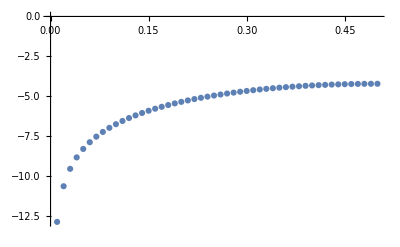

```mathematica
{(#[[1]])/200,-1/2(#[[2]])/(p1P*p2P)*4Pi*(1/p1P+1/p2P-1)/.{p1P->(#[[1]])/200,p2P->(200-#[[1]])/200}}&/@fp1Plus
ListPlot[%]
```

```mathematica
T1={(#[[1]])/200,-Pi(#[[2]])/(p1P*p2P)^2*(1+p1P^2+p2P^2)/.{p1P->(#[[1]])/200,p2P->(200-#[[1]])/200}}&/@fp1Plus
ListPlot[T1]
```

{{1/100,-12.839170829333},{1/50,-10.610660608959},{3/100,-9.5228358874475},{1/25,-8.8088466247567},{1/20,-8.2792449308898},{3/50,-7.8592776309514},{7/100,-7.5120037648262},{2/25,-7.2165167628209},{9/100,-6.9598528288935},{1/10,-6.7334255958772},{11/100,-6.531257236871},{3/25,-6.3490202347619},{13/100,-6.1834818032085},{7/50,-6.0321638249342},{3/20,-5.8931252797395},{4/25,-5.7648178098524},{17/100,-5.6459867961847},{9/50,-5.5356017665313},{19/100,-5.4328062885938},{1/5,-5.336881151662},{21/100,-5.2472168231592},{11/50,-5.1632925125713},{23/100,-5.0846600292748},{6/25,-5.0109311760768},{1/4,-4.9417677894628},{13/50,-4.8768737879418},{27/100,-4.8159887628262},{7/25,-4.7588827672121},{29/100,-4.7053520454877},{3/10,-4.6552155082641},{31/100,-4.6083118034211},{8/25,-4.5644968678937},{33/100,-4.5236418702361},{17/50,-4.4856314732291},{7/20,-4.4503623604896},{9/25,-4.4177419823656},{37/100,-4.387687485208},{19/50,-4.3601247950146},{39/100,-4.3349878318988},{2/5,-4.3122178361762},{41/100,-4.2917627903526},{21/50,-4.27357692411},{43/100,-4.2576202916885},{11/25,-4.2438584129455},{9/20,-4.2322619709408},{23/50,-4.2228065602079},{47/100,-4.2154724809809},{12/25,-4.2102445756052},{49/100,-4.2071121041897},{1/2,-4.2060686573032}}

-Graphics-

{{1/100,7.90947},{1/50,8.42602},{3/100,8.72501},{1/25,8.93524},{1/20,9.09684},{3/50,9.22764},{7/100,9.33714},{2/25,9.43101},{9/100,9.51292},{1/10,9.58536},{11/100,9.65011},{3/25,9.70848},{13/100,9.76147},{7/50,9.80987},{3/20,9.85427},{4/25,9.89518},{17/100,9.93299},{9/50,9.96805},{19/100,10.0006},{1/5,10.031},{21/100,10.0593},{11/50,10.0857},{23/100,10.1104},{6/25,10.1336},{1/4,10.1552},{13/50,10.1755},{27/100,10.1945},{7/25,10.2123},{29/100,10.2289},{3/10,10.2445},{31/100,10.259},{8/25,10.2725},{33/100,10.2852},{17/50,10.2969},{7/20,10.3077},{9/25,10.3178},{37/100,10.327},{19/50,10.3355},{39/100,10.3432},{2/5,10.3502},{41/100,10.3564},{21/50,10.362},{43/100,10.3669},{11/25,10.3711},{9/20,10.3746},{23/50,10.3775},{47/100,10.3797},{12/25,10.3813},{49/100,10.3823},{1/2,10.3826}}

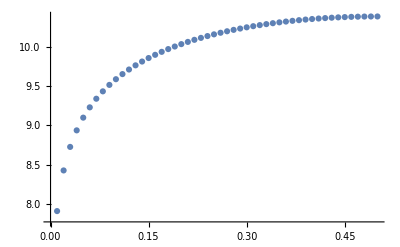

```mathematica
T2={(#[[1]])/200,Log[√((#[[1]])/200*(1-(#[[1]])/200))#[[2]]]}&/@detTable
ListPlot[T2]
```

{{1/100,-107.753},{1/50,-111.723},{3/100,-114.223},{1/25,-116.032},{1/20,-117.441},{3/50,-118.591},{7/100,-119.558},{2/25,-120.389},{9/100,-121.115},{1/10,-121.758},{11/100,-122.333},{3/25,-122.851},{13/100,-123.321},{7/50,-123.751},{3/20,-124.144},{4/25,-124.507},{17/100,-124.842},{9/50,-125.152},{19/100,-125.44},{1/5,-125.709},{21/100,-125.959},{11/50,-126.192},{23/100,-126.41},{6/25,-126.614},{1/4,-126.804},{13/50,-126.983},{27/100,-127.15},{7/25,-127.306},{29/100,-127.452},{3/10,-127.589},{31/100,-127.716},{8/25,-127.835},{33/100,-127.946},{17/50,-128.048},{7/20,-128.143},{9/25,-128.231},{37/100,-128.312},{19/50,-128.386},{39/100,-128.453},{2/5,-128.514},{41/100,-128.569},{21/50,-128.617},{43/100,-128.66},{11/25,-128.697},{9/20,-128.728},{23/50,-128.753},{47/100,-128.772},{12/25,-128.786},{49/100,-128.794},{1/2,-128.797}}

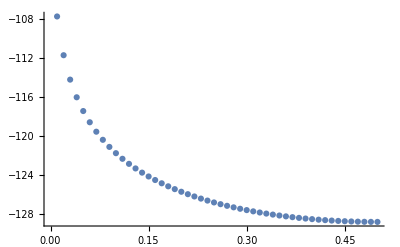

```mathematica
MapThread[{#1[[1]],#1[[2]]-12#2[[2]]}&,{T1,T2}]
ListPlot[%]
```

```mathematica
Manipulate[ListPlot[MapThread[{#1[[1]],#1[[2]]+a#2[[2]]}&,{T1,T2}],PlotRange->All],{a,-3,-4}]
```

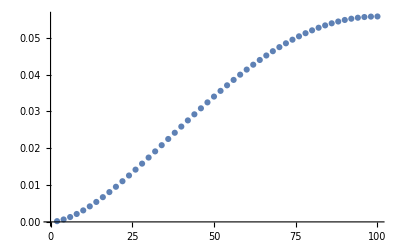

```mathematica
ListPlot[%341]
```

```mathematica
1/p1P+1/p2P-1/pP//Together
```

(-p1P p2P+p1P pP+p2P pP)/(p1P p2P pP)

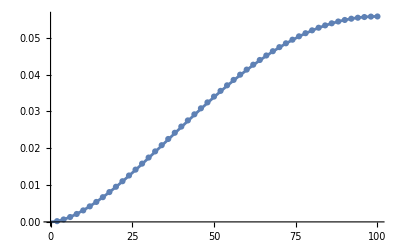

```mathematica
Show[%362,Plot[0.05578471814947499614730876597528202376`14.68321513480475((x(200-x))/(200/2(200-200/2)))^(26/15),{x,0,100}]]
```

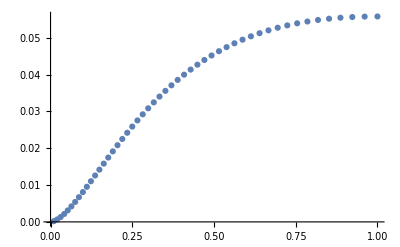

```mathematica
ListPlot[{(#[[1]])/(200-#[[1]]),#[[2]]}&/@%341]
```

```mathematica
Monitor[Table[{2j,Det[Developer`ToPackedArray[RedMMatrixN[{2j,200-2j}],Real]]},{j,1,50}],j]
```

{{2,27366.6},{4,32602.},{6,36080.8},{8,38758.},{10,40960.1},{12,42842.2},{14,44491.4},{16,45961.8},{18,47289.7},{20,48500.5},{22,49613.1},{24,50641.5},{26,51596.8},{28,52487.6},{30,53321.1},{32,54102.9},{34,54837.8},{36,55530.},{38,56182.6},{40,56798.8},{42,57381.},{44,57931.4},{46,58451.9},{48,58944.2},{50,59409.7},{52,59849.7},{54,60265.4},{56,60657.9},{58,61028.1},{60,61376.7},{62,61704.6},{64,62012.5},{66,62300.8},{68,62570.2},{70,62821.2},{72,63054.1},{74,63269.5},{76,63467.6},{78,63648.7},{80,63813.3},{82,63961.4},{84,64093.4},{86,64209.4},{88,64309.6},{90,64394.2},{92,64463.2},{94,64516.8},{96,64555.},{98,64577.9},{100,64585.5}}

```mathematica
detTable=%365
```

{{2,27366.6},{4,32602.},{6,36080.8},{8,38758.},{10,40960.1},{12,42842.2},{14,44491.4},{16,45961.8},{18,47289.7},{20,48500.5},{22,49613.1},{24,50641.5},{26,51596.8},{28,52487.6},{30,53321.1},{32,54102.9},{34,54837.8},{36,55530.},{38,56182.6},{40,56798.8},{42,57381.},{44,57931.4},{46,58451.9},{48,58944.2},{50,59409.7},{52,59849.7},{54,60265.4},{56,60657.9},{58,61028.1},{60,61376.7},{62,61704.6},{64,62012.5},{66,62300.8},{68,62570.2},{70,62821.2},{72,63054.1},{74,63269.5},{76,63467.6},{78,63648.7},{80,63813.3},{82,63961.4},{84,64093.4},{86,64209.4},{88,64309.6},{90,64394.2},{92,64463.2},{94,64516.8},{96,64555.},{98,64577.9},{100,64585.5}}

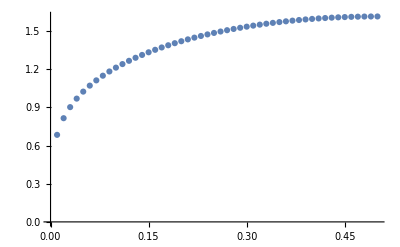

```mathematica
ListPlot[{(#[[1]])/200,(#[[2]])/200^2}&/@%365]
```

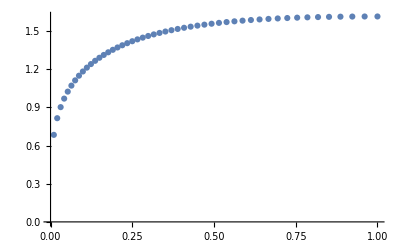

```mathematica
ListPlot[{(#[[1]])/(200-#[[1]]),(#[[2]])/200^2}&/@%365]
```

```mathematica
Monitor[Table[{8j,Det[Developer`ToPackedArray[RedMMatrixN[{4j,4j}],Real]],Det[Developer`ToPackedArray[RedMMatrixN[{6j,2j}],Real]]},{j,2,50,2}],j]
```

{{16,219.743,202.047},{32,1045.59,961.698},{48,2603.71,2394.94},{64,4974.08,4575.35},{80,8217.97,7559.27},{96,12385.8,11393.1},{112,17520.9,16116.7},{128,23661.3,21765.},{144,30841.3,28369.6},{160,39091.9,35959.},{176,48441.9,44559.7},{192,58917.6,54196.},{208,70544.,64890.7},{224,83344.3,76665.2},{240,97340.5,89539.7},{256,112553.,103533.},{272,129003.,118664.},{288,146707.,134950.},{304,165685.,152408.},{320,185954.,171052.},{336,207530.,190899.},{352,230430.,211964.},{368,254669.,234260.},{384,280262.,257802.},{400,307223.,282603.}}

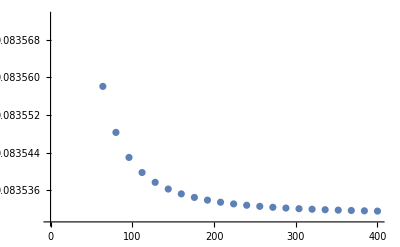

```mathematica
ListPlot[{#[[1]],Log[(#[[2]])/(#[[3]])]}&/@%388]
```

```mathematica
Monitor[Table[{8j,Det[Developer`ToPackedArray[RedMMatrixN[{4j,4j}],Real]],Det[Developer`ToPackedArray[RedMMatrixN[{7j,1j}],Real]]},{j,2,50,2}],j]
```

{{16,219.743,173.538},{32,1045.59,827.214},{48,2603.71,2060.62},{64,4974.08,3937.06},{80,8217.97,6505.02},{96,12385.8,9804.42},{112,17520.9,13869.5},{128,23661.3,18730.5},{144,30841.3,24414.4},{160,39091.9,30946.},{176,48441.9,38347.8},{192,58917.6,46640.8},{208,70544.,55844.7},{224,83344.3,65977.9},{240,97340.5,77057.8},{256,112553.,89100.9},{272,129003.,102123.},{288,146707.,116139.},{304,165685.,131162.},{320,185954.,147208.},{336,207530.,164289.},{352,230430.,182417.},{368,254669.,201605.},{384,280262.,221866.},{400,307223.,243209.}}

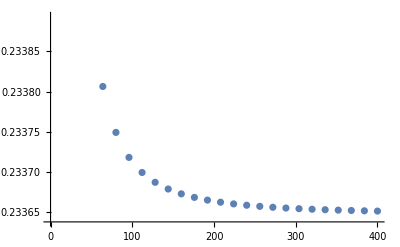

```mathematica
ListPlot[{#[[1]],Log[(#[[2]])/(#[[3]])]}&/@%386]
```

```mathematica
Jvector[{10,10},{p1,p2}][[1]].PseudoInverse[MMatrixN[{10,10}]].Jvector[{10,10},{p1,p2}][[1]]//FullSimplify
```

0.2459623807969 p1^2-0.4919247615938 p1 p2+0.2459623807969 p2^2

```mathematica
Jvector[{20,20},{p1,p2}][[1]].PseudoInverse[MMatrixN[{20,20}]].Jvector[{20,20},{p1,p2}][[1]]//FullSimplify
```

0.2332173830611 p1^2-0.4664347661221 p1 p2+0.2332173830611 p2^2

```mathematica
Jvector[{30,30},{p1,p2}][[1]].PseudoInverse[MMatrixN[{30,30}]].Jvector[{30,30},{p1,p2}][[1]]//FullSimplify
```

0.2290052887004 p1^2-0.4580105774008 p1 p2+0.2290052887004 p2^2

```mathematica
Jvector[{100,100},{p1,p2}][[1]].PseudoInverse[MMatrixN[{100,100}]].Jvector[{100,100},{p1,p2}][[1]]//FullSimplify
```

0.223138872598 p1^2-0.446277745196 p1 p2+0.223138872598 p2^2

```mathematica
0.05578471814947499614730876597528202376`14.68321513480475 * 2^2(p1-p2)^2//Expand
```

0.2231388725979 p1^2-0.4462777451958 p1 p2+0.2231388725979 p2^2

```mathematica
Jvector[{40,160},{p1,p2}][[1]].PseudoInverse[MMatrixN[{40,160}]].Jvector[{40,160},{p1,p2}][[1]]//FullSimplify
```

0.6471550598 p1^2-0.3235775299 p1 p2+0.04044719124 p2^2

```mathematica
0.02588620239180119311760031958400601025`14.69875937564892 * (200)^2(p1/40-p2/160)^2//Expand
```

0.64715505979503 p1^2-0.32357752989751 p1 p2+0.040447191237189 p2^2

```mathematica
Monitor[Table[{20n,RedJMJ[{10n,10n}]},{n,1,16}],n]
```

{{20,0.061490595199231},{40,0.058304345765266},{60,0.057251322175105},{80,0.056726512847629},{100,0.056412172342143},{120,0.056202839178113},{140,0.056053426770934},{160,0.05594142832674},{180,0.055854354493163},{200,0.055784718149475},{220,0.055727757983085},{240,0.05568030150685},{260,0.05564015336131},{280,0.055605746016265},{300,0.055575930312764},{320,0.055549844615697}}

```mathematica
Monitor[Table[{20n,RedJMJ[{4n,16n}]},{n,1,16}],n]
```

{{20,0.029576301433574},{40,0.027508154352279},{60,0.026828792791887},{80,0.026491010551635},{100,0.026288950337382},{120,0.026154497607835},{140,0.026058584460866},{160,0.025986717718187},{180,0.025930861737159},{200,0.025886202391801},{220,0.025849679748587},{240,0.025819255777984},{260,0.025793520630827},{280,0.025771467925356},{300,0.025752360054866},{320,0.025735644076401}}

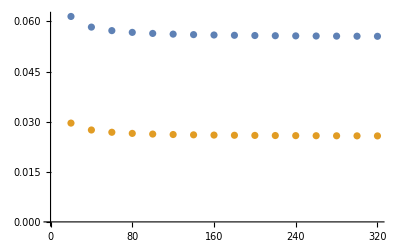

```mathematica
ListPlot[{%311,%313}]
```

```mathematica
103/80//N
```

1.2875

```mathematica
116/90//N
```

1.28889

```mathematica
128.796/100
```

1.28796

```mathematica
Det[RedMMatrixN[{40,50}]]/90
Times@@(MMatrixN[{40,50}]//Eigenvalues)[[;;-2]]
```

118.58334040331

118.5833404033

```mathematica
Det[RedMMatrixN[{40,60}]]
Times@@(MMatrixN[{40,60}]//Eigenvalues)[[;;-2]]
```

13414.972935948

134.1497293595

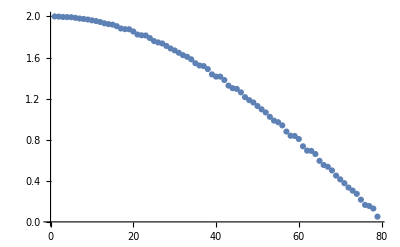

```mathematica
ListPlot[(MMatrixN[{44,36}]//Eigenvalues)[[;;-2]]]
```

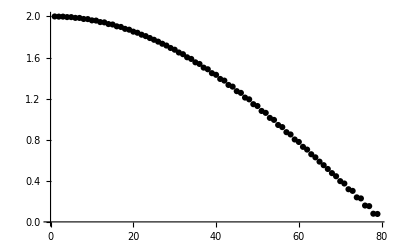

```mathematica
ListPlot[(MMatrixN[{2,78}]//Eigenvalues)[[;;-2]],PlotStyle->Black]
```

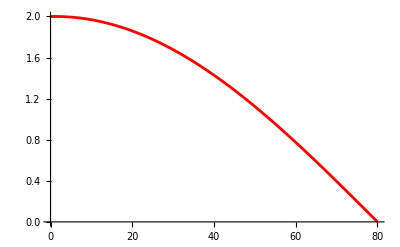

```mathematica
Plot[2Cos[Pi/2 (x-1)/79],{x,0,80},PlotStyle->Red]
```

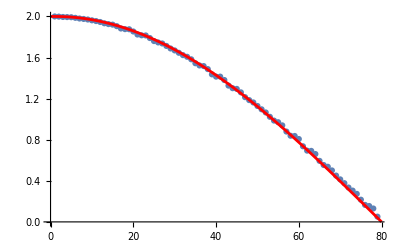

```mathematica
Show[%235,%250]
```

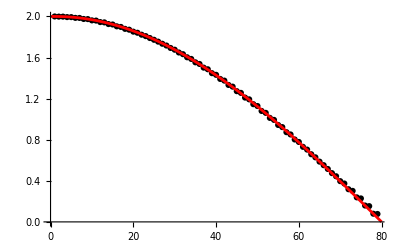

```mathematica
Show[%248,%250]
```

```mathematica
Table[{10n,Log[Times@@(MMatrixN[{4n,6n}]//Eigenvalues)[[;;-2]]]},{n,1,10}]
```

{{10,2.0196066191374},{20,2.8868852430187},{30,3.3938749279823},{40,3.753533067339},{50,4.032488243091},{60,4.260404176236},{70,4.453100962141},{80,4.620020679218},{90,4.767253228742},{100,4.898956559423}}

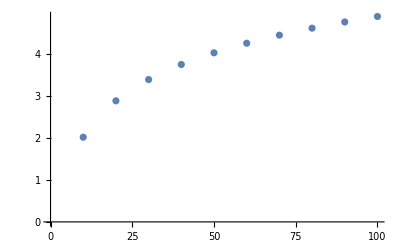

```mathematica
ListPlot[%228]
```

```mathematica
Table[{10n,Log[Times@@(MMatrixN[{2n,8n}]//Eigenvalues)[[;;-2]]]},{n,1,10}]
```

{{10,1.9012995253765},{20,2.7699536747184},{30,3.2772140052717},{40,3.636968211273},{50,3.915968095681},{60,4.143908380521},{70,4.336619872179},{80,4.503549142933},{90,4.650788246566},{100,4.782496267432}}

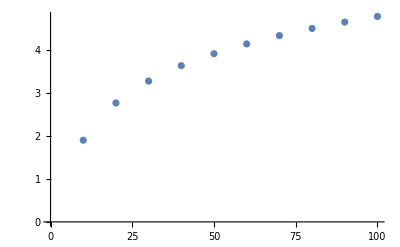

```mathematica
ListPlot[%231]
```

### Fixing wavefunctional normalization and showing eigenvalues

```mathematica
singleMMatrixN[{L1_,L2_}]:=Module[{Mkernel,Mkernel1,Mkernel2,k1,k2,M,L=L1+L2},
Mkernel=Table[N[Mkernelfunc[L,x],prec],{x,0,L-1}];
Mkernel1=Table[N[Mkernelfunc[L1,x],prec],{x,0,L1-1}];
Mkernel2=Table[N[Mkernelfunc[L2,x],prec],{x,0,L2-1}];
k1=Table[k*χ[{L1,L2},1][k],{k,1,L}];
k2=Table[(k-L1)*χ[{L1,L2},2][k],{k,1,L}];

M=Table[
(*multiply by Pi to kill exponential scaling of det*)
Pi*N[2/(Pi*L)Mkernel[[Mod[k-l,L]+1]],prec]
,{k,1,L},
{l,1,L}];
Return[M,Module];
];
```

```mathematica
Product[2Sin[m Pi/L],{m,1,L-1}]
```

L

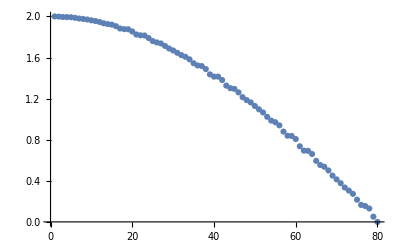

```mathematica
MMatrixN[{44,36}]//Eigenvalues//ListPlot
```

```mathematica
orderingList[L_]:=Join[{{0,1}},Table[{(-1)^(2k)Floor[k/2],k},{k,2,L-1}]]
```

```mathematica
orderList[list_]:=Map[{#1[[1]],list[[#1[[2]]]]}&,orderingList[(list//Length)+1]]
```

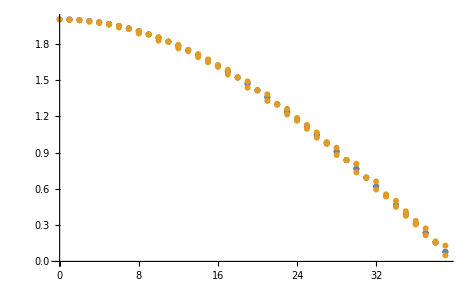

```mathematica
ListPlot[{orderList[(singleMMatrixN[{44,36}]//Eigenvalues)[[;;-2]]],orderList[(MMatrixN[{44,36}]//Eigenvalues)[[;;-2]]]}]
```

### Scaling of det’M

```mathematica
Monitor[Table[{4j,1/(4j)Det[Developer`ToPackedArray[RedMMatrixNFast[{2j,2j}],Real]]},{j,1,300,10}]
,j]
```

{{4,2.41421},{44,48.6532},{84,109.185},{124,177.661},{164,251.983},{204,331.021},{244,414.052},{284,500.572},{324,590.201},{364,682.645},{404,777.67},{444,875.079},{484,974.71},{524,1076.42},{564,1180.1},{604,1285.63},{644,1392.92},{684,1501.89},{724,1612.47},{764,1724.59},{804,1838.18},{844,1953.2},{884,2069.59},{924,2187.3},{964,2306.3},{1004,2426.53},{1044,2547.97},{1084,2670.58},{1124,2794.32},{1164,2919.17}}

```mathematica
LinearModelFit[{Log[#[[1]]],Log[#[[2]]]}&/@%161,{1,x},x]
```

FittedModel[…]

```mathematica
%262["BestFitParameters"]
```

{-0.849727,1.25068}

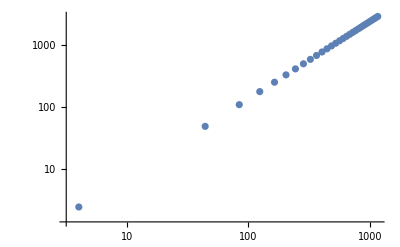

```mathematica
ListLogLogPlot[%161]
```

```mathematica
detMlist={#[[1]],(#[[2]])/(#[[1]])^(5/4)}&/@%161
```

{{4,0.426777},{44,0.429334},{84,0.429351},{124,0.429354},{164,0.429356},{204,0.429356},{244,0.429357},{284,0.429357},{324,0.429357},{364,0.429357},{404,0.429357},{444,0.429357},{484,0.429357},{524,0.429357},{564,0.429357},{604,0.429357},{644,0.429357},{684,0.429357},{724,0.429357},{764,0.429357},{804,0.429357},{844,0.429357},{884,0.429357},{924,0.429357},{964,0.429357},{1004,0.429357},{1044,0.429357},{1084,0.429357},{1124,0.429357},{1164,0.429357}}

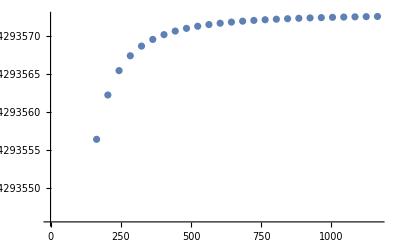

```mathematica
ListPlot[detMlist]
```

```mathematica
derDetMlist=MapThread[{#1[[1]],#2}&,{detMlist[[;;-2]],1/40Differences[detMlist[[;;,2]]]}];
```

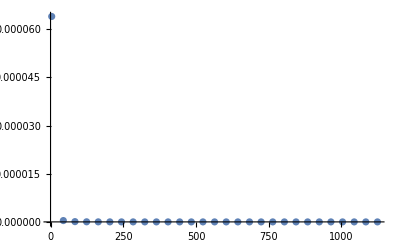

```mathematica
ListPlot[derDetMlist,PlotRange->All]
```

```mathematica
Monitor[Table[{6j,1/(6j)Det[Developer`ToPackedArray[RedMMatrixNFast[{2j,4j}],Real]]},{j,1,200,8}]
,j]
```

{{6,3.88059},{54,60.714},{102,134.45},{150,217.735},{198,308.069},{246,404.097},{294,504.953},{342,610.028},{390,718.866},{438,831.113},{486,946.483},{534,1064.74},{582,1185.69},{630,1309.16},{678,1435.01},{726,1563.11},{774,1693.34},{822,1825.61},{870,1959.82},{918,2095.9},{966,2233.77},{1014,2373.37},{1062,2514.62},{1110,2657.49},{1158,2801.9}}

```mathematica
LinearModelFit[{Log[#[[1]]],Log[#[[2]]]}&/@%167,{1,x},x]
```

FittedModel[…]

```mathematica
%266["BestFitParameters"]
```

{-0.882974,1.25047}

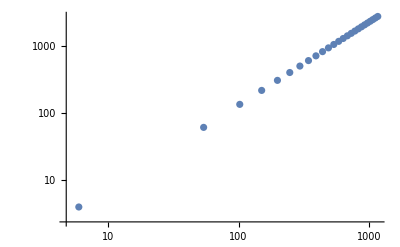

```mathematica
ListLogLogPlot[%167]
```

```mathematica
detMlist2={#[[1]],(#[[2]])/(#[[1]])^(5/4)}&/@%167
```

{{6,0.413246},{54,0.41476},{102,0.414774},{150,0.414777},{198,0.414778},{246,0.414779},{294,0.414779},{342,0.414779},{390,0.414779},{438,0.41478},{486,0.41478},{534,0.41478},{582,0.41478},{630,0.41478},{678,0.41478},{726,0.41478},{774,0.41478},{822,0.41478},{870,0.41478},{918,0.41478},{966,0.41478},{1014,0.41478},{1062,0.41478},{1110,0.41478},{1158,0.41478}}

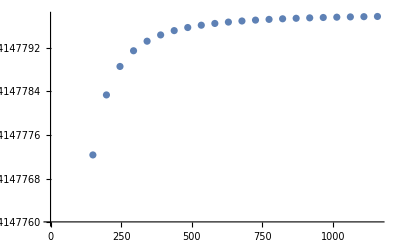

```mathematica
ListPlot[detMlist2]
```

```mathematica
Monitor[Table[{20j,1/(20j)Det[Developer`ToPackedArray[RedMMatrixNFast[{2j,18j}],Real]]},{j,1,50,1}]
,j]
```

{{20,13.5995},{40,32.4119},{60,53.8258},{80,77.1303},{100,101.951},{120,128.051},{140,155.266},{160,183.473},{180,212.577},{200,242.503},{220,273.187},{240,304.577},{260,336.628},{280,369.303},{300,402.566},{320,436.389},{340,470.745},{360,505.61},{380,540.963},{400,576.784},{420,613.056},{440,649.763},{460,686.889},{480,724.421},{500,762.346},{520,800.652},{540,839.329},{560,878.365},{580,917.752},{600,957.479},{620,997.539},{640,1037.92},{660,1078.62},{680,1119.64},{700,1160.95},{720,1202.56},{740,1244.46},{760,1286.64},{780,1329.1},{800,1371.84},{820,1414.84},{840,1458.11},{860,1501.63},{880,1545.41},{900,1589.44},{920,1633.71},{940,1678.23},{960,1722.98},{980,1767.97},{1000,1813.18}}

```mathematica
LinearModelFit[{Log[#[[1]]],Log[#[[2]]]}&/@%170,{1,x},x]
```

FittedModel[…]

```mathematica
%269["BestFitParameters"]
```

{-1.13367,1.25029}

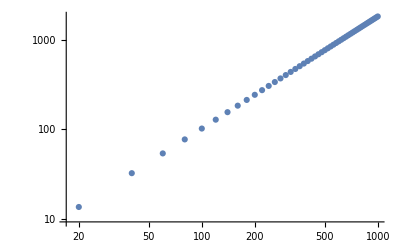

```mathematica
ListLogLogPlot[%170]
```

```mathematica
detMlist3={#[[1]],(#[[2]])/(#[[1]])^(5/4)}&/@%170
```

{{20,0.321541},{40,0.322203},{60,0.322331},{80,0.322376},{100,0.322397},{120,0.322409},{140,0.322415},{160,0.32242},{180,0.322423},{200,0.322425},{220,0.322427},{240,0.322428},{260,0.322429},{280,0.32243},{300,0.32243},{320,0.322431},{340,0.322431},{360,0.322432},{380,0.322432},{400,0.322432},{420,0.322432},{440,0.322433},{460,0.322433},{480,0.322433},{500,0.322433},{520,0.322433},{540,0.322433},{560,0.322433},{580,0.322433},{600,0.322434},{620,0.322434},{640,0.322434},{660,0.322434},{680,0.322434},{700,0.322434},{720,0.322434},{740,0.322434},{760,0.322434},{780,0.322434},{800,0.322434},{820,0.322434},{840,0.322434},{860,0.322434},{880,0.322434},{900,0.322434},{920,0.322434},{940,0.322434},{960,0.322434},{980,0.322434},{1000,0.322434}}

### Testing convergence of J M J

```mathematica
Monitor[Table[{20j,RedJMJFast[{2j,18j}]},{j,1,40,2}],j]
```

{{20,0.011659663285119},{60,0.010073936258475},{100,0.0097669073062399},{140,0.0096363944089457},{180,0.0095641662544517},{220,0.0095183068219612},{260,0.0094866053780314},{300,0.0094633823080825},{340,0.0094456375703772},{380,0.0094316371883567},{420,0.0094203091181231},{460,0.0094109549079424},{500,0.0094031000011727},{540,0.0093964106782668},{580,0.0093906454191663},{620,0.0093856251196172},{660,0.0093812141522305},{700,0.0093773079289926},{740,0.0093738245023192},{780,0.0093706987532973}}

{a→0.04504459306779,b→0.80609160414894,c→0.0093128537727639}

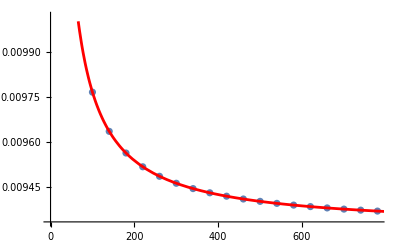

```mathematica
fitform=c+a/(L-b);
fit=FindFit[%394,fitform,{a,b,c},L]
Show[ListPlot[%394],Plot[fitform/.fit,{L,1,800},PlotStyle->Red]]
Clear[fit,fitform]
```

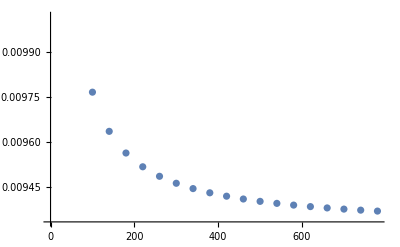

```mathematica
ListPlot[%394]
```

```mathematica
-1/Pi x(1-x)(x Log[x]+(1-x)Log[1-x])/.x->1/10
%//N
```

-(9 (-9/10 Log[10/9]-Log[10]/10))/(100 π)

0.00931294

```mathematica
Monitor[Table[{4j,RedJMJFast[{2j,2j}]},{j,1,200,10}],j]
```

{{4,0.088388347648318},{44,0.05801670747731},{84,0.056651632783926},{124,0.056169092786492},{164,0.055922311854903},{204,0.055772431479694},{244,0.055671744780958},{284,0.055599446614858},{324,0.055545014242781},{364,0.055502553618507},{404,0.055468506478757},{444,0.055440597570972},{484,0.055417304197899},{524,0.055397568839715},{564,0.055380634121157},{604,0.05536594338295},{644,0.055353078322368},{684,0.055341718522661},{724,0.055331614402971},{764,0.055322568668565}}

{a→0.12506587135336,b→0.23631179111616,c→0.055158743858505}

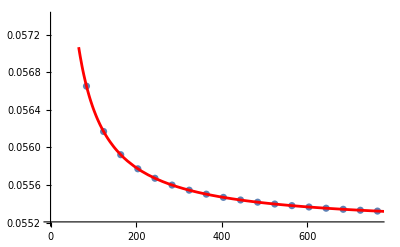

```mathematica
fitform=c+a/(L-b);
fit=FindFit[%225,fitform,{a,b,c},L]
Show[ListPlot[%225],Plot[fitform/.fit,{L,1,800},PlotStyle->Red]]
Clear[fit,fitform]
```

```mathematica
-1/Pi x(1-x)(x Log[x]+(1-x)Log[1-x])/.x->1/2
%//N
```

Log[2]/(4 π)

0.0551589

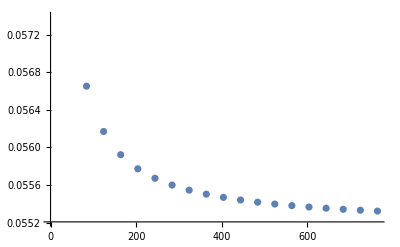

```mathematica
ListPlot[%225]
```

```mathematica
Monitor[Table[{2j,RedJMJFast[{2j,400-2j}]},{j,2,100,2}],j]
```

{{4,0.00018911895759006},{8,0.00063642053765606},{12,0.001284731699831},{16,0.0021010601681314},{20,0.0030611294940639},{24,0.0041454320285372},{28,0.0053375294768463},{32,0.006623152067347},{36,0.0079896592358757},{40,0.0094256893297857},{44,0.010920918300068},{48,0.012465885891139},{52,0.01405186598588},{56,0.015670767118117},{60,0.017315054337654},{64,0.018977686639304},{68,0.020652066021833},{72,0.022331995424073},{76,0.024011643563279},{80,0.025685515227715},{84,0.027348425941384},{88,0.028995480178562},{92,0.030622052493739},{96,0.032223771070983},{100,0.033796503300239},{104,0.035336343066595},{108,0.036839599498838},{112,0.038302786970539},{116,0.039722616183696},{120,0.041095986194249},{124,0.04241997726216},{128,0.043691844427678},{132,0.044909011730829},{136,0.046069067003784},{140,0.047169757176257},{144,0.048208984042728},{148,0.049184800447648},{152,0.050095406850859},{156,0.050939148240767},{160,0.051714511367201},{164,0.052420122269776},{168,0.053054744080907},{172,0.053617275085492},{176,0.054106747021891},{180,0.05452232361104},{184,0.054863299302605},{188,0.055129098228893},{192,0.055319273358919},{196,0.055433505846563},{200,0.055471604568199}}

```mathematica
fp1Plus={(#[[1]])/400,#[[2]]}&/@%219
```

{{1/100,0.00018911895759006},{1/50,0.00063642053765606},{3/100,0.001284731699831},{1/25,0.0021010601681314},{1/20,0.0030611294940639},{3/50,0.0041454320285372},{7/100,0.0053375294768463},{2/25,0.006623152067347},{9/100,0.0079896592358757},{1/10,0.0094256893297857},{11/100,0.010920918300068},{3/25,0.012465885891139},{13/100,0.01405186598588},{7/50,0.015670767118117},{3/20,0.017315054337654},{4/25,0.018977686639304},{17/100,0.020652066021833},{9/50,0.022331995424073},{19/100,0.024011643563279},{1/5,0.025685515227715},{21/100,0.027348425941384},{11/50,0.028995480178562},{23/100,0.030622052493739},{6/25,0.032223771070983},{1/4,0.033796503300239},{13/50,0.035336343066595},{27/100,0.036839599498838},{7/25,0.038302786970539},{29/100,0.039722616183696},{3/10,0.041095986194249},{31/100,0.04241997726216},{8/25,0.043691844427678},{33/100,0.044909011730829},{17/50,0.046069067003784},{7/20,0.047169757176257},{9/25,0.048208984042728},{37/100,0.049184800447648},{19/50,0.050095406850859},{39/100,0.050939148240767},{2/5,0.051714511367201},{41/100,0.052420122269776},{21/50,0.053054744080907},{43/100,0.053617275085492},{11/25,0.054106747021891},{9/20,0.05452232361104},{23/50,0.054863299302605},{47/100,0.055129098228893},{12/25,0.055319273358919},{49/100,0.055433505846563},{1/2,0.055471604568199}}

```mathematica
T1={#[[1]],(-Pi/(p1P p2P)^2(1+(p1P)^2+(p2P)^2)/.{p1P->#[[1]],p2P->(1-#[[1]])})*#[[2]]}&/@fp1Plus;
```

```mathematica
{(#[[1]])/200,Log[#[[2]]]}&/@detTable
```

{{1/100,10.2171},{1/50,10.3921},{3/100,10.4935},{1/25,10.5651},{1/20,10.6204},{3/50,10.6653},{7/100,10.7031},{2/25,10.7356},{9/100,10.764},{1/10,10.7893},{11/100,10.812},{3/25,10.8325},{13/100,10.8512},{7/50,10.8683},{3/20,10.8841},{4/25,10.8986},{17/100,10.9121},{9/50,10.9247},{19/100,10.9364},{1/5,10.9473},{21/100,10.9575},{11/50,10.967},{23/100,10.976},{6/25,10.9843},{1/4,10.9922},{13/50,10.9996},{27/100,11.0065},{7/25,11.013},{29/100,11.0191},{3/10,11.0248},{31/100,11.0301},{8/25,11.0351},{33/100,11.0397},{17/50,11.044},{7/20,11.048},{9/25,11.0517},{37/100,11.0552},{19/50,11.0583},{39/100,11.0611},{2/5,11.0637},{41/100,11.066},{21/50,11.0681},{43/100,11.0699},{11/25,11.0715},{9/20,11.0728},{23/50,11.0738},{47/100,11.0747},{12/25,11.0753},{49/100,11.0756},{1/2,11.0757}}

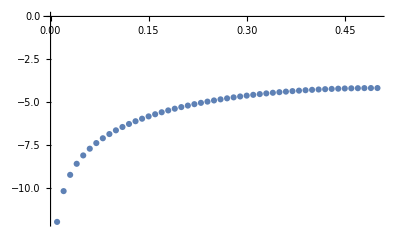

```mathematica
ListPlot[T1]
```

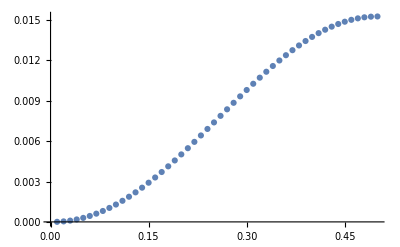

```mathematica
ListPlot[{#[[1]],Exp[#[[2]]]}&/@T1]
```

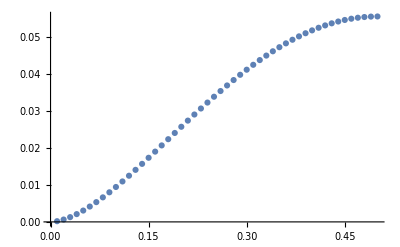

```mathematica
ListPlot[fp1Plus]
```

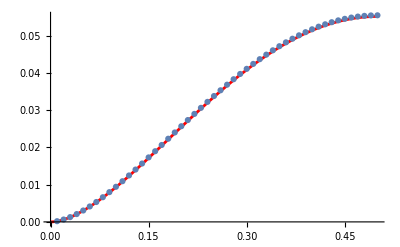

```mathematica
Show[Plot[-1/Pi x(1-x)(x Log[x]+(1-x)Log[1-x]),{x,0,1/2},PlotStyle->Red],ListPlot[fp1Plus]]
```

```mathematica
((-1/Pi x(1-x)(x Log[x]+(1-x)Log[1-x])/.x->#[[1]])-#[[2]])&/@fp1Plus
```

{-0.00001264312152663,-0.00002476688545928,-0.00003663956110292,-0.00004826211819226,-0.0000596346795932,-0.0000707572757786,-0.0000816299171964,-0.0000922526082069,-0.00010262535089,-0.000112748146339,-0.000122620995172,-0.000132243897762,-0.000141616854342,-0.000150739865066,-0.000159612930036,-0.000168236049324,-0.000176609222983,-0.00018473245105,-0.000192605733551,-0.00020022907051,-0.00020760246194,-0.000214725907855,-0.000221599408265,-0.000228222963177,-0.000234596572597,-0.000240720236531,-0.000246593954983,-0.000252217727955,-0.000257591555452,-0.000262715437474,-0.000267589374025,-0.000272213365105,-0.000276587410716,-0.000280711510859,-0.000284585665536,-0.000288209874746,-0.000291584138491,-0.000294708456772,-0.000297582829589,-0.000300207256942,-0.000302581738832,-0.000304706275258,-0.000306580866223,-0.000308205511725,-0.000309580211765,-0.000310704966342,-0.000311579775458,-0.000312204639112,-0.000312579557305,-0.000312704530036}

### Comparison to Weyl Factor

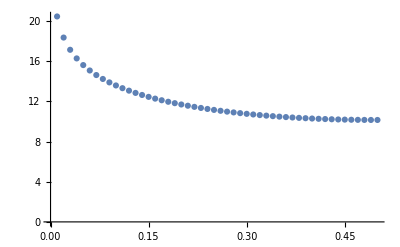

```mathematica
ListPlot[{(#[[1]])/200,-12Log[(#[[2]])/200^(9/4)]}&/@detTable]
```

```mathematica
detTable2=Monitor[Table[{4j,Det[Developer`ToPackedArray[RedMMatrixNFast[{4j,400-4j}],Real]]},{j,1,50}],j]
```

{{4,130440.},{8,155164.},{12,171671.},{16,184390.},{20,194857.},{24,203805.},{28,211647.},{32,218640.},{36,224955.},{40,230714.},{44,236005.},{48,240897.},{52,245440.},{56,249678.},{60,253642.},{64,257360.},{68,260856.},{72,264148.},{76,267253.},{80,270184.},{84,272953.},{88,275571.},{92,278047.},{96,280388.},{100,282603.},{104,284696.},{108,286673.},{112,288540.},{116,290301.},{120,291959.},{124,293519.},{128,294983.},{132,296355.},{136,297636.},{140,298830.},{144,299938.},{148,300963.},{152,301905.},{156,302767.},{160,303549.},{164,304254.},{168,304882.},{172,305434.},{176,305910.},{180,306313.},{184,306641.},{188,306896.},{192,307078.},{196,307187.},{200,307223.}}

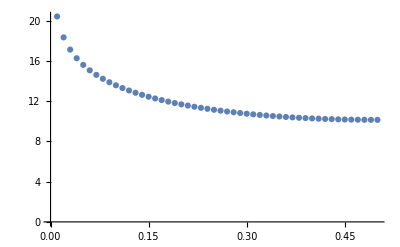

```mathematica
ListPlot[{(#[[1]])/400,-12Log[(#[[2]])/400^(9/4)]}&/@detTable2]
```

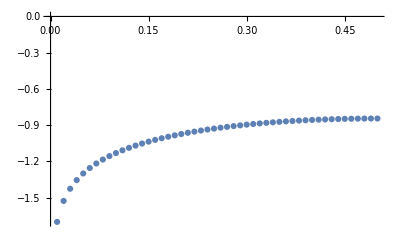

```mathematica
ListPlot[{(#[[1]])/400,Log[(#[[2]])/400^(9/4)]}&/@detTable2]
```

```mathematica
Manipulate[Show[Plot[a+Log[Exp[-2(-x Log[x]-(1-x)Log[(1-x)])*(1-1/x-1/(1-x))]/(x(1-x))],{x,0.01,1/2},PlotRange->All],%346],{a,0,5}]
```

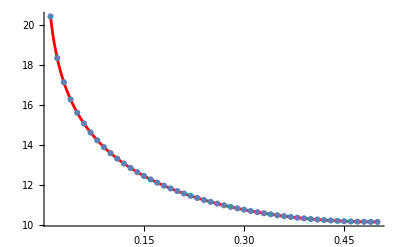

```mathematica
Show[Plot[4.6+Log[Exp[-2(-x Log[x]-(1-x)Log[(1-x)])*(1-1/x-1/(1-x))]/(x(1-x))],{x,0.01,1/2},PlotRange->All,PlotStyle->Red],%346]
```

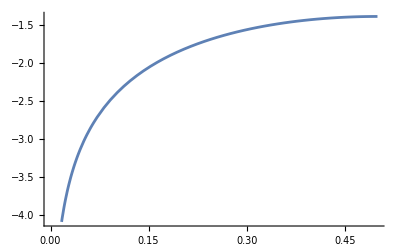

```mathematica
Plot[Log[x(1-x)],{x,0,1/2}]
```

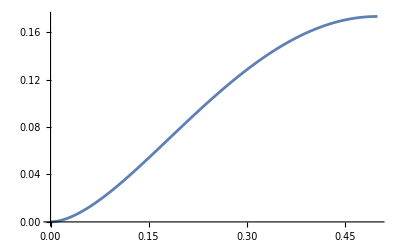

```mathematica
Plot[-x(1-x)(x Log[x]+(1-x)Log[1-x]),{x,0,1/2}]
```

### Seeing the 1/(x(1-x)):

```mathematica
detTable2
```

{{4,130440.},{8,155164.},{12,171671.},{16,184390.},{20,194857.},{24,203805.},{28,211647.},{32,218640.},{36,224955.},{40,230714.},{44,236005.},{48,240897.},{52,245440.},{56,249678.},{60,253642.},{64,257360.},{68,260856.},{72,264148.},{76,267253.},{80,270184.},{84,272953.},{88,275571.},{92,278047.},{96,280388.},{100,282603.},{104,284696.},{108,286673.},{112,288540.},{116,290301.},{120,291959.},{124,293519.},{128,294983.},{132,296355.},{136,297636.},{140,298830.},{144,299938.},{148,300963.},{152,301905.},{156,302767.},{160,303549.},{164,304254.},{168,304882.},{172,305434.},{176,305910.},{180,306313.},{184,306641.},{188,306896.},{192,307078.},{196,307187.},{200,307223.}}

```mathematica
fp1Plus
```

{{1/100,0.00018911895759006},{1/50,0.00063642053765606},{3/100,0.001284731699831},{1/25,0.0021010601681314},{1/20,0.0030611294940639},{3/50,0.0041454320285372},{7/100,0.0053375294768463},{2/25,0.006623152067347},{9/100,0.0079896592358757},{1/10,0.0094256893297857},{11/100,0.010920918300068},{3/25,0.012465885891139},{13/100,0.01405186598588},{7/50,0.015670767118117},{3/20,0.017315054337654},{4/25,0.018977686639304},{17/100,0.020652066021833},{9/50,0.022331995424073},{19/100,0.024011643563279},{1/5,0.025685515227715},{21/100,0.027348425941384},{11/50,0.028995480178562},{23/100,0.030622052493739},{6/25,0.032223771070983},{1/4,0.033796503300239},{13/50,0.035336343066595},{27/100,0.036839599498838},{7/25,0.038302786970539},{29/100,0.039722616183696},{3/10,0.041095986194249},{31/100,0.04241997726216},{8/25,0.043691844427678},{33/100,0.044909011730829},{17/50,0.046069067003784},{7/20,0.047169757176257},{9/25,0.048208984042728},{37/100,0.049184800447648},{19/50,0.050095406850859},{39/100,0.050939148240767},{2/5,0.051714511367201},{41/100,0.052420122269776},{21/50,0.053054744080907},{43/100,0.053617275085492},{11/25,0.054106747021891},{9/20,0.05452232361104},{23/50,0.054863299302605},{47/100,0.055129098228893},{12/25,0.055319273358919},{49/100,0.055433505846563},{1/2,0.055471604568199}}

{{1/100,8.42159},{1/50,8.13764},{3/100,7.87443},{1/25,7.6629},{1/20,7.4896},{3/50,7.34406},{7/100,7.21928},{2/25,7.11053},{9/100,7.01452},{1/10,6.92886},{11/100,6.85178},{3/25,6.78193},{13/100,6.71825},{7/50,6.65992},{3/20,6.60627},{4/25,6.55673},{17/100,6.51086},{9/50,6.46828},{19/100,6.42866},{1/5,6.39174},{21/100,6.35727},{11/50,6.32507},{23/100,6.29494},{6/25,6.26674},{1/4,6.24034},{13/50,6.21561},{27/100,6.19245},{7/25,6.17077},{29/100,6.15047},{3/10,6.1315},{31/100,6.11378},{8/25,6.09726},{33/100,6.08187},{17/50,6.06758},{7/20,6.05434},{9/25,6.04211},{37/100,6.03085},{19/50,6.02054},{39/100,6.01115},{2/5,6.00265},{41/100,5.99502},{21/50,5.98825},{43/100,5.9823},{11/25,5.97718},{9/20,5.97287},{23/50,5.96936},{47/100,5.96663},{12/25,5.96469},{49/100,5.96353},{1/2,5.96314}}

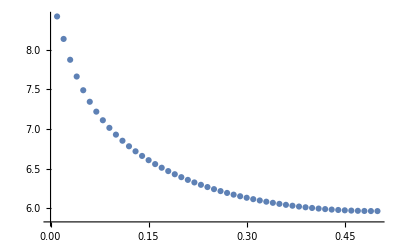

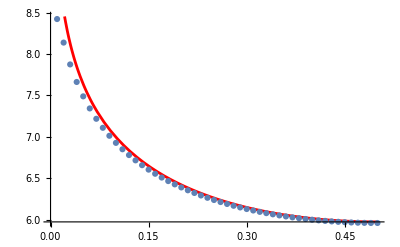

```mathematica
T3=MapThread[{(#1[[1]])/400,-12Log[(#1[[2]])/400^(9/4)]+-1/2(#2[[2]])/(p1P*p2P)*4Pi*(1/p1P+1/p2P-1)/.{p1P->#2[[1]],p2P->1-#2[[1]]}}&,{detTable2,fp1Plus}]
ListPlot[T3]
Show[Plot[4.59-Log[x(1-x)],{x,0,1/2},PlotStyle->Red],ListPlot[T3]]
```

### Scaling and matching of f_1 M J

```mathematica
Monitor[Table[{4j,1/Abs[RedvMJ[{2j,2j},Table[N[Exp[-2 Pi I k/(4j)]-1,prec],{k,1,4j-1}]]]},{j,1,151,10}],j]
```

{{4,8.},{44,12.1227},{84,12.3328},{124,12.4078},{164,12.4464},{204,12.4699},{244,12.4856},{284,12.497},{324,12.5055},{364,12.5122},{404,12.5176},{444,12.522},{484,12.5256},{524,12.5287},{564,12.5314},{604,12.5337}}

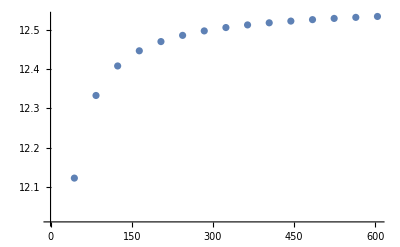

```mathematica
ListPlot[%574]
```

```mathematica
Monitor[
Table[{2k,Abs[RedvMJ[{2k,200-2k},Table[N[Exp[2 Pi I j/200]-1,prec],{j,1,199}]]]^2},{k,1,50}],k]
```

{{2,2.8227×10^-6},{4,0.0000120303},{6,0.0000285353},{8,0.0000530975},{10,0.0000863649},{12,0.000128888},{14,0.000181124},{16,0.00024344},{18,0.000316115},{20,0.000399338},{22,0.000493213},{24,0.000597754},{26,0.000712889},{28,0.000838463},{30,0.000974235},{32,0.00111988},{34,0.00127501},{36,0.00143913},{38,0.0016117},{40,0.0017921},{42,0.00197964},{44,0.00217359},{46,0.00237314},{48,0.00257743},{50,0.00278558},{52,0.00299665},{54,0.00320967},{56,0.00342364},{58,0.00363755},{60,0.00385037},{62,0.00406106},{64,0.00426857},{66,0.00447189},{68,0.00466998},{70,0.00486184},{72,0.00504649},{74,0.00522298},{76,0.00539041},{78,0.00554789},{80,0.00569462},{82,0.00582982},{84,0.00595279},{86,0.00606287},{88,0.00615948},{90,0.00624211},{92,0.00631033},{94,0.00636377},{96,0.00640214},{98,0.00642525},{100,0.00643297}}

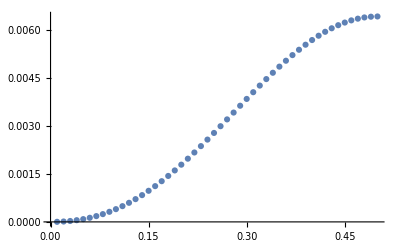

```mathematica
ListPlot[{(#[[1]])/200,#[[2]]}&/@%571]
```

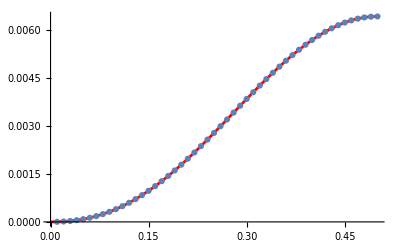

```mathematica
Show[Plot[%571[[-1,2]]4 x^(-2x)(1-x)^(-2(1-x))(x(1-x))^2,{x,0,1/2},PlotStyle->Red],ListPlot[{(#[[1]])/200,#[[2]]}&/@%571]]
```

```mathematica
Monitor[
Table[{2k,(400)^3Abs[RedvMJ[{2k,400-2k},Table[N[Exp[2 Pi I j/400]-1,prec],{j,1,399}]]]^2},{k,2,100,2}],k]
```

{{4,179.15},{8,763.724},{12,1811.66},{16,3371.22},{20,5483.55},{24,8183.58},{28,11500.4},{32,15457.2},{36,20071.9},{40,25356.4},{44,31317.2},{48,37955.3},{52,45266.1},{56,53239.8},{60,61861.},{64,71109.4},{68,80959.4},{72,91380.9},{76,102339.},{80,113794.},{84,125703.},{88,138018.},{92,150689.},{96,163661.},{100,176879.},{104,190281.},{108,203807.},{112,217394.},{116,230977.},{120,244491.},{124,257869.},{128,271046.},{132,283957.},{136,296535.},{140,308718.},{144,320443.},{148,331650.},{152,342281.},{156,352281.},{160,361598.},{164,370184.},{168,377992.},{172,384982.},{176,391116.},{180,396364.},{184,400695.},{188,404089.},{192,406525.},{196,407993.},{200,408482.}}

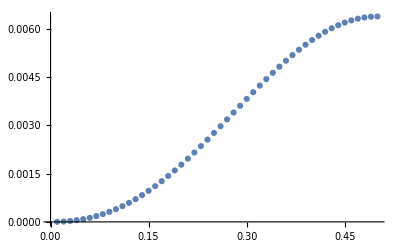

```mathematica
ListPlot[{(#[[1]])/400,(#[[2]])/400^3}&/@%553]
```

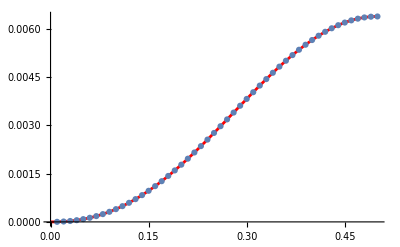

```mathematica
Show[Plot[{(%553[[-1,2]])/400^3 4 x^(-2x)(1-x)^(-2(1-x))(x(1-x))^2},{x,0,1/2},PlotStyle->Red],ListPlot[{(#[[1]])/400,(#[[2]])/400^3}&/@%553]]
```